```mathematica
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["pdfLaTeX" -> "/usr/local/bin/pdflatex"];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}];
```

## Energy control

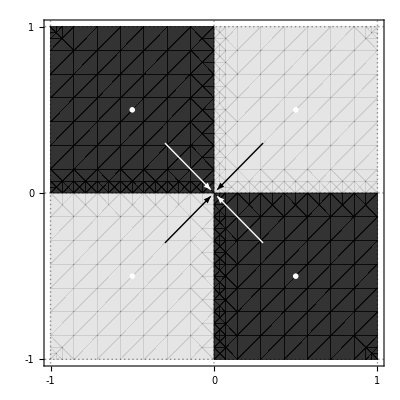

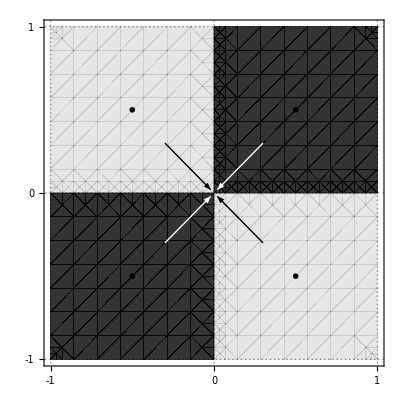

```mathematica
energyControl1 = ContourPlot[x*y, {x, -1, 1}, {y, -1, 1},
Contours->1,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->1.5],MaTeX[ "E",Magnification->1.5]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
FrameTicksStyle->Directive[FontSize->16],
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
White,
Text[MaTeX["+a_{max}",Magnification->2], {.5, .5}],Text[MaTeX["+a_{max}",Magnification->2], {-.5, -.5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {.5, -.5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {-.5, .5}],
Arrow[{{-.3, .3}, {-.02, .02}}],
Arrow[{{.3, -.3}, {.02, -.02}}],
Black,
Arrow[{{.3, .3}, {.02, .02}}],
Arrow[{{-.3, -.3}, {-.02, -.02}}]
}
]

energyControl2 = ContourPlot[-x*y, {x, -1, 1}, {y, -1, 1},
Contours->1,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->1.5],MaTeX[ "E",Magnification->1.5]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
FrameTicksStyle->Directive[FontSize->16],
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
Black,
Text[MaTeX["+a_{max}",Magnification->2], {-.5, .5}],Text[MaTeX["+a_{max}",Magnification->2], {.5, -.5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {.5, .5}],
Text[MaTeX["\\color{white}-a_{max}",Magnification->2], {-.5, -.5}],
Arrow[{{-.3, .3}, {-.02, .02}}],
Arrow[{{.3, -.3}, {.02, -.02}}],
White,
Arrow[{{.3, .3}, {.02, .02}}],
Arrow[{{-.3, -.3}, {-.02, -.02}}]
}
]
```

```mathematica
Export[NotebookDirectory[]<>"../energy-control1.pdf",energyControl1,"PDF"]
Export[NotebookDirectory[]<>"../energy-control2.pdf",energyControl2,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control1.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control2.pdf

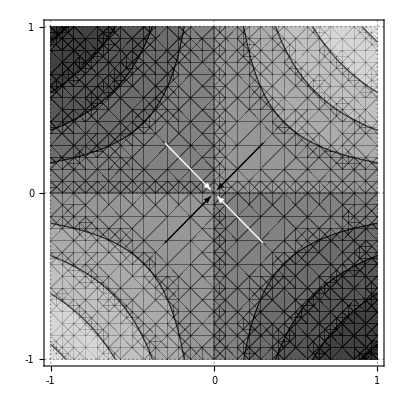

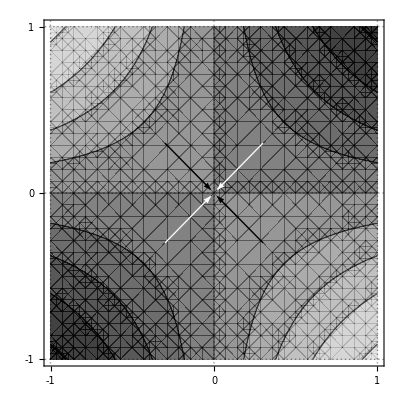

```mathematica
energyControl3 = ContourPlot[Tanh[x*y], {x, -1, 1}, {y, -1, 1},
Contours->10,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->1.5],MaTeX[ "E",Magnification->1.5]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
FrameTicksStyle->Directive[FontSize->16],
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
White,
Arrow[{{-.3, .3}, {-.02, .02}}],
Arrow[{{.3, -.3}, {.02, -.02}}],
Black,
Arrow[{{.3, .3}, {.02, .02}}],
Arrow[{{-.3, -.3}, {-.02, -.02}}]
}
]

energyControl4 = ContourPlot[-Tanh[x*y], {x, -1, 1}, {y, -1, 1},
Contours->10,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX["\\dot \\theta",Magnification->1.5],MaTeX[ "E",Magnification->1.5]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
FrameTicksStyle->Directive[FontSize->16],
GridLines->{{0, -1, 1}, {0, -1, 1}},
Method->{"TransparentPolygonMesh"->True},
Epilog->{
Black,
Arrow[{{-.3, .3}, {-.02, .02}}],
Arrow[{{.3, -.3}, {.02, -.02}}],
White,
Arrow[{{.3, .3}, {.02, .02}}],
Arrow[{{-.3, -.3}, {-.02, -.02}}]
}
]
```

```mathematica
Export[NotebookDirectory[]<>"../energy-control3.pdf",energyControl3,"PDF"]
Export[NotebookDirectory[]<>"../energy-control4.pdf",energyControl4,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control3.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../energy-control4.pdf

## Cogging Torque

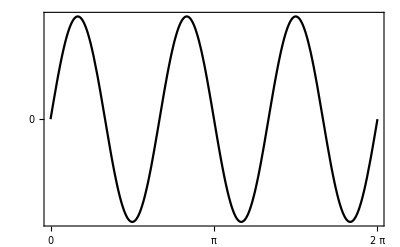

```mathematica
coggingTorque = Plot[Sin[3*x], {x, 0, 2Pi},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{Placed[LineLegend[{MaTeX[TeXForm[Subscript[τ, c]],Magnification->2]}], {.85, .9}]},
PlotRange->{5, -5},
FrameLabel ->{MaTeX["\\text{Angolo}",Magnification->1.5], MaTeX["\\text{Coppia}",Magnification->1.5]},
FrameTicks->{{{0}, None}, {{0, Pi, 2Pi}, None}},
FrameTicksStyle->Directive[FontSize->16],
GridLines->{{0, Pi, 2Pi}, {0}}
]
```

```mathematica
Export[NotebookDirectory[]<>"../cogging-torque.pdf",coggingTorque,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../cogging-torque.pdf

## Parametri motore

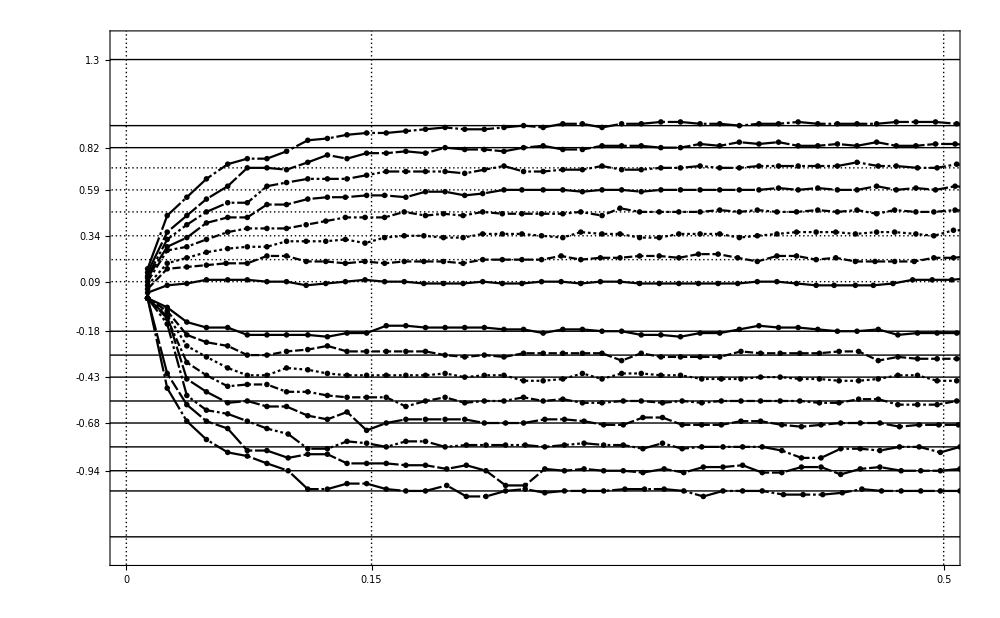

```mathematica
data = {};
plotLegend = {};
For [i = 4, i < 12, i++,
AppendTo[data, Import[NotebookDirectory[]<>"../../data/"<>ToString[i]<>".csv"]];
AppendTo[plotLegend,MaTeX[ToString[i*15 //IntegerPart]<>"", Magnification->1.5]];
];
For [i = 4, i < 12, i++,
AppendTo[data, Import[NotebookDirectory[]<>"../../data/"<>ToString[-i]<>".csv"]];
AppendTo[plotLegend,MaTeX[ToString[-i*15 //IntegerPart]<>"", Magnification->1.5]];
];

motorPlot1 = ListLinePlot[
data,
InterpolationOrder->1,
PlotRange->{{0, .5}, {-1.4, 1.4}},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
ImageSize->{1000, 500},
PlotLegends->plotLegend,
FrameTicksStyle->Directive[FontSize->16],
FrameTicks->{{{.09, .21, .34, .47, .59, .71, .82, .94, -.18, -.31, -.43, -.56, -.68, -.81, -.94, -1.05, 1.3, -1.3}, None}, {0, .15, .5}},
GridLines->{{0, .15, .5}, {.09, .21, .34, .47, .59, .71, .82, .94, -.18, -.31, -.43, -.56, -.68, -.81, -.94, -1.05, 1.3, -1.3} },
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Velocità }\\left(\\frac m s\\right)",Magnification->1.5]}
]
```

```mathematica
Export[NotebookDirectory[]<>"../motor-vmax-fit.pdf",motorPlot1,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../motor-vmax-fit.pdf

y

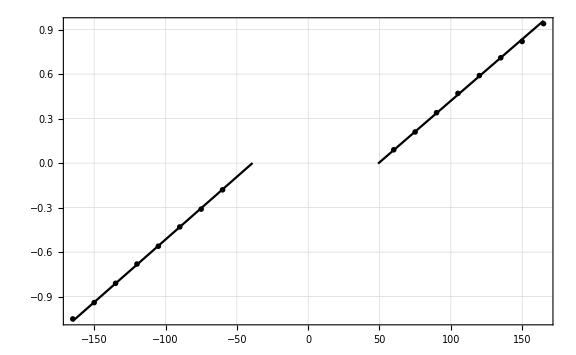

```mathematica
lineFitData = { 
{-165, -1.05},
{-150, -.94},
{-135, -.81},
{-120, -.68},
{-105, -.56},
{-90, -.43},
{-75, -.31},
{-60, -.18},
{60, .09},
{75, .21},
{90, .34},
{105, .47},
{120, .59},
{135, .71},
{150, .82},
{165, .94}
};

listPltot1= ListPlot[
lineFitData,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid", "Large"},
FrameTicksStyle->Directive[FontSize->16],
FrameLabel ->{MaTeX["\\text{PWM}",Magnification->1.5], MaTeX["\\text{Velocità massima }\\left(\\frac m s\\right)",Magnification->1.5]}
];
y
linePlot1 = Plot[.00845x + .33, {x, -165, -39}, PlotTheme->"Monochrome"];
linePlot2 = Plot[.00830x - .41, {x, 49, 165}, PlotTheme->"Monochrome",  PlotLegends->{MaTeX["v_{\\max} = \\left\\{\\begin{aligned} .00845u &+ .33, \\ u < -39 \\\\ .00830u &- .41 , \\ u > 49\\end{aligned} \\right.", Magnification->1.5]}];
motorPlot2 = Show[listPltot1, linePlot1, linePlot2]
```

```mathematica
Export[NotebookDirectory[]<>"../motor-offset.pdf",motorPlot2,"PDF"]
B=120
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../motor-offset.pdf

120

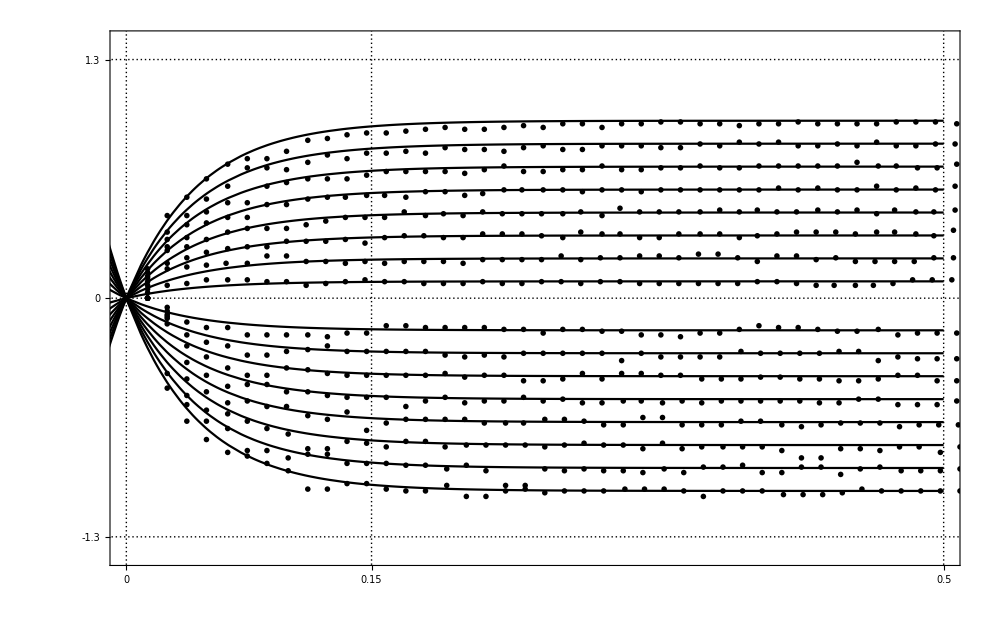

```mathematica
data = {};
plotLegend = {};
For [i = 4, i < 12, i++,
AppendTo[data, Import[NotebookDirectory[]<>"../../data/"<>ToString[i]<>".csv"]];
AppendTo[plotLegend,MaTeX[ToString[i*15 //IntegerPart]<>"", Magnification->1.5]];
];
For [i = 4, i < 12, i++,
AppendTo[data, Import[NotebookDirectory[]<>"../../data/"<>ToString[-i]<>".csv"]];
AppendTo[plotLegend,MaTeX[ToString[-i*15 //IntegerPart]<>"", Magnification->1.5]];
];

listPlot2 = ListPlot[
data,
InterpolationOrder->1,
PlotRange->{{0, .5}, {-1.4, 1.4}},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
ImageSize->{1000, 500},
PlotLegends->plotLegend,
FrameTicksStyle->Directive[FontSize->16],
FrameTicks->{{{0, 1.3, -1.3}, None}, {0, .15, .5}},
GridLines->{{0, .15, .5}, {0, 1.3, -1.3} },
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Velocità }\\left(\\frac m s\\right)",Magnification->1.5]}
];

B=120;
tau=23;
expoPlots = {};
For [i = 4, i < 12, i++,
AppendTo[
expoPlots,
Plot[(i*15/B-49/B)(1-E^-(tau x)), {x, -1, .5}, PlotTheme->"Monochrome"]
];
];
For [i = 4, i < 12, i++,
AppendTo[
expoPlots,
Plot[(-i*15/B+39/B)(1-E^-(tau x)), {x, -1, .5}, PlotTheme->"Monochrome"]
]
];

motorPlot3 = Show[listPlot2, expoPlots]
```

```mathematica
Export[NotebookDirectory[]<>"../motor-expo-fit.pdf",motorPlot3,"PDF"]
Solve[B/(a m) == tau, a] /. params
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../motor-expo-fit.pdf

{{a→237.154}}

## Grafici simulazioni

Per usare questi grafici è necessario aprire il "notebook dei calcoli"/Users/matteo/repo/uni/dpic/docs/report/assets/source/calcoli.nbNone/Users/matteo/repo/uni/dpic/docs/report/assets/source/calcoli.nb ed eseguire il codice, in modo che siano definite le funzioni corrette.

0.0243628 (1-Cos[θ[t]])+0.105 x'[t]^2+0.000039541 θ'[t]^2+0.011 (0.012769 Sin[θ[t]]^2 θ'[t]^2+(x'[t]+0.113 Cos[θ[t]] θ'[t])^2)

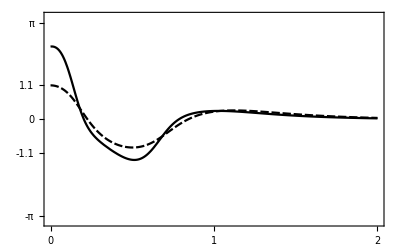

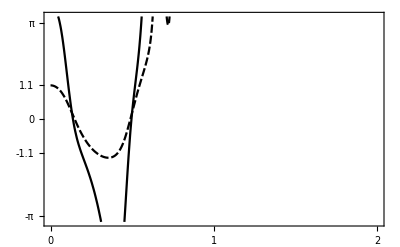

```mathematica
s[t_]:= {x[t],  x'[t], θ[t], θ'[t] };
T = 2;

Klqr1 = LQRegulatorGains[ssm /. params, {Q, R} /. {r11->1, q11->1} /. params];
solutionsLQR1 = simulateSystem[-Klqr1.s[t], T, {0, 0, 1.1,0}];

Klqr2 = LQRegulatorGains[ssm /. params, {Q, R} /. {r11->.1, q11->1} /. params];
solutionsLQR2 = simulateSystem[-Klqr2.s[t], T, {0, 0, 1.1,0}];

v2 = (x'[t] + l θ'[t]*Cos[θ[t]])^2 + ( l θ'[t]*Sin[θ[t]])^2;
Kin = 1/2 *M*x'[t]^2       + 1/2* m*v2    + 1/2*(J - m l^2)*θ'[t]^2 ;
V = m*g*l*(1-Cos[θ[t]]);
Energy = Kin + V /. params


occBlowup1= Plot[{
-Klqr1.solutionsLQR1/Pi,
solutionsLQR1[[3]]
},
{t, 0, T},
PlotRange->{-Pi-.2, Pi+.2},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{MaTeX["f_{LQR}\\left(N /\pi\\right)",Magnification->1.5],MaTeX["\\theta_{LQR}(rad)",Magnification->1.5]},
FrameTicks->{{{0, Pi, -Pi, -1.1, 1.1}, None}, {{0, 1, 2}, None}},
GridLines->{{0,1, 2}, {0, Pi, -1.1, 1.1, -Pi} },
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5]}
]

occBlowup2= Plot[{
-Klqr2.solutionsLQR2/Pi,
solutionsLQR2[[3]]
},
{t, 0, T},
PlotRange->{-Pi-.2, Pi+.2},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{MaTeX["f_{LQR}\\left(N /\pi\\right)",Magnification->1.5],MaTeX["\\theta_{LQR}(rad)",Magnification->1.5]},
FrameTicks->{{{0, Pi, -Pi, -1.1, 1.1}, None}, {{0, 1, 2}, None}},
GridLines->{{0,1, 2}, {0, Pi, -1.1, 1.1, -Pi} },
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5]}
]
(*
energyPlot= Plot[{
Energy /.{x[t] -> solutionsLQR1[[1]], x'[t]->solutionsLQR1[[2]], θ[t]->solutionsLQR1[[3]], θ'[t]->solutionsLQR1[[4]]},
Energy /.{x[t] -> solutionsLQR2[[1]], x'[t]->solutionsLQR2[[2]], θ[t]->solutionsLQR2[[3]], θ'[t]->solutionsLQR2[[4]]}
},
{t, 0, T},
PlotRange->{-Pi-.2, Pi+.2},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{MaTeX["f_{LQR}\\left(N /\pi\\right)",Magnification->1.5],MaTeX["\\theta_{LQR}(rad)",Magnification->1.5]},
FrameTicks->{{{0, Pi, -Pi, -1, 1}, None}, {{0, 1, 2}, None}},
GridLines->{{0,1, 2}, {0, Pi, -1, 1, -Pi} },
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5]}
]*)
```

```mathematica
series = Series[motionEquations[[2, 2]], {θ[t], 0, 3}] /. {u[t]->0, θ'[t]->0} /. params
Solve[(Energy /. {x[t] -> 0, x'[t]->0, θ[t]->1, θ'[t]->0}) == (Energy /. {x[t] -> 0, x'[t]->0, θ[t]->0, θ'[t]->s}),s] 
Energy /. {x[t] -> 0, x'[t]->0, θ[t]->1, θ'[t]->0}
Export[NotebookDirectory[]<>"../occasional-blowup-r1.pdf",occBlowup1,"PDF"]
Export[NotebookDirectory[]<>"../occasional-blowup-r.1.pdf",occBlowup2,"PDF"]
```

73.0823 θ[t]-18.0204 θ[t]^3+O[θ[t]]^4

{{s→-7.88794},{s→7.88794}}

0.0111995

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../occasional-blowup-r1.pdf

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../occasional-blowup-r.1.pdf

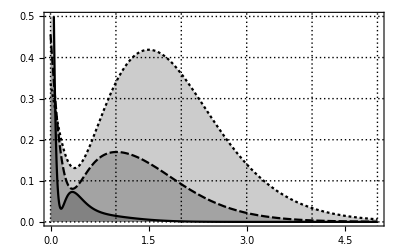

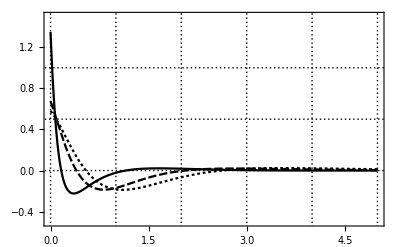

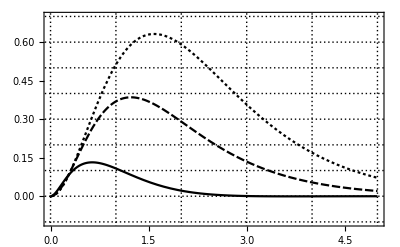

```mathematica
s[t_]:= {x[t],  x'[t], θ[t], θ'[t] };
T = 5;

Klqr = LQRegulatorGains[ssm /. params, {Q, R} /. params];
solutionsLQR = simulateSystem[-Klqr.s[t], T, {0, 0, .2 ,0}];

Krandom = StateFeedbackGains[ssm /. params, {-1, -2, -3, -4}];
solutionsRandom = simulateSystem[-Krandom.s[t], T, {0, 0, .2,0}];

Krandom2 = StateFeedbackGains[ssm /. params, {-1.5, -1, -3, -2}];
solutionsRandom2 = simulateSystem[-Krandom2.s[t], T, {0, 0, .2,0}];


Plot[{
costIntegrand[t, -Klqr.solutionsLQR, solutionsLQR],
costIntegrand[t, -Krandom.solutionsRandom, solutionsRandom],
costIntegrand[t, -Krandom2.solutionsRandom2, solutionsRandom2]
},
{t, 0, T},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
Filling->Axis,
PlotRange->{0, .5},
GridLines->{{0,1 , 2, 3, 4, 5}, {0, .1, .2, .3, .4,.5}},
PlotLegends->{MaTeX["K_{LQR}",Magnification->1.5],MaTeX["K_{1}",Magnification->1.5],MaTeX["K_{2}",Magnification->1.5]},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Costo istantaneo}",Magnification->1.5]}
]

Plot[{
 -Klqr.solutionsLQR,

 -Krandom.solutionsRandom,

-Krandom2.solutionsRandom2
},
{t, 0, T},
PlotRange->{-.5, 1.5},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
GridLines->{{0,1 , 2, 3, 4, 5}, {0, .5, 1}},
PlotLegends->{MaTeX["f_{LQR}",Magnification->1.5],MaTeX["f_{1}",Magnification->1.5],MaTeX["f_{2}",Magnification->1.5]},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Forza subita }(N)",Magnification->1.5]}
]

Plot[{
solutionsLQR[[1]],
 solutionsRandom[[1]],
solutionsRandom2[[1]]
},
{t, 0, T},
PlotRange->{-.1, .7},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
GridLines->{{0,1 , 2, 3, 4, 5}, {0, .1, .2, .3,.4, .5, .6, .7, -.1}},
PlotLegends->{MaTeX["q_{LQR}",Magnification->1.5],MaTeX["q_{1}",Magnification->1.5],MaTeX["q_{2}",Magnification->1.5]},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Posizione }(m)",Magnification->1.5]}
]
```

```mathematica
(*Ottimalità*)
Klqr
Eigenvalues[A-B.Klqr] /. params
Jlqr = NIntegrate[costIntegrand[t, -Klqr.solutionsLQR, solutionsLQR], {t, 0, T}];
Jrandom1 = NIntegrate[costIntegrand[t, -Krandom.solutionsRandom, solutionsRandom], {t, 0, T}];
Jrandom2 = NIntegrate[costIntegrand[t, -Krandom.solutionsRandom2, solutionsRandom2], {t, 0, T}];
Jrandom1/Jlqr
Jrandom2/Jlqr
(*todo print graphs*)
```

{{-1.,-1.06992,-6.74594,-0.799319}}

{-8.55825-0.0184522 ⅈ,-8.55825+0.0184522 ⅈ,-1.79823-1.03305 ⅈ,-1.79823+1.03305 ⅈ}

3.24016

8.80445

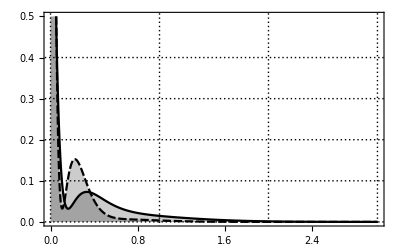

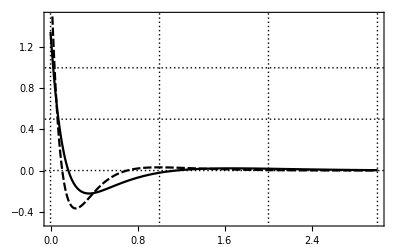

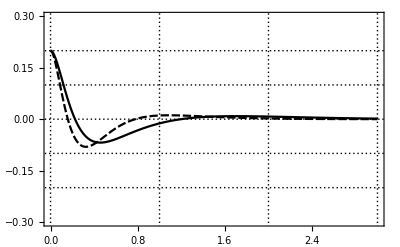

```mathematica
s[t_]:= {x[t],  x'[t], θ[t], θ'[t] };
T = 3;

Klqr = LQRegulatorGains[ssm /. params, {Q, R} /. params];
solutionsLQR = simulateSystem[-Klqr.s[t], T, {0, 0, .2 ,0}];

Kfast = StateFeedbackGains[ssm /. params, {-10, -9, -3, -4}];
solutionsFast = simulateSystem[-Kfast.s[t], T, {0, 0, .2 ,0}];


Plot[{
costIntegrand[t, -Klqr.solutionsLQR, solutionsLQR],
costIntegrand[t, -Kfast.solutionsFast, solutionsFast]
},
{t, 0,T},
PlotRange->{0, .5},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
Filling->Axis,
PlotLegends->{MaTeX["K_{LQR}",Magnification->1.5],MaTeX["K_{fast}",Magnification->1.5]},
GridLines->{{0,1 , 2, 3, 4, 5}, {0, .1, .2, .3, .4}},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Costo istantaneo}",Magnification->1.5]}
]

Plot[{
 -Klqr.solutionsLQR,

 -Kfast.solutionsFast
},
{t, 0, T},
PlotRange->{-.5, 1.5},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{MaTeX["f_{LQR}",Magnification->1.5],MaTeX["f_{fast}",Magnification->1.5]},
GridLines->{{0,1 , 2, 3, 4, 5}, {0, .5, 1}},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel->{MaTeX["\\text{Tempo }(s)",Magnification->1.5],MaTeX["\\text{Forza subita }(N)",Magnification->1.5]}
]

Plot[{
solutionsLQR[[3]],
 solutionsFast[[3]]
},
{t, 0, T},
PlotRange->{-.3, .3},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{MaTeX["\\theta_{LQR}",Magnification->1.5],MaTeX["\\theta_{fast}",Magnification->1.5]},
GridLines->{{0,1 , 2, 3, 4, 5}, {0, .1, .2, -.1, -.2}},
FrameTicksStyle->Directive[FontSize->13],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Angolo }(rad)",Magnification->1.5]}
]
```

```mathematica
(*Aha questa funzione è più fast*)
Eigenvalues[A-B.K] /. params

Jlqr = NIntegrate[costIntegrand[t, -Klqr.solutionsLQR, solutionsLQR], {t, 0, T}];
Jfast = NIntegrate[costIntegrand[t, -Kfast.solutionsFast, solutionsFast], {t, 0, T}];
Jfast/Jlqr
(*todo print graphs*)
```

{-8.55825-0.0184522 ⅈ,-8.55825+0.0184522 ⅈ,-1.79823-1.03305 ⅈ,-1.79823+1.03305 ⅈ}

1.29223

InterpolatingFunction::dmval: Input value {5.00048} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

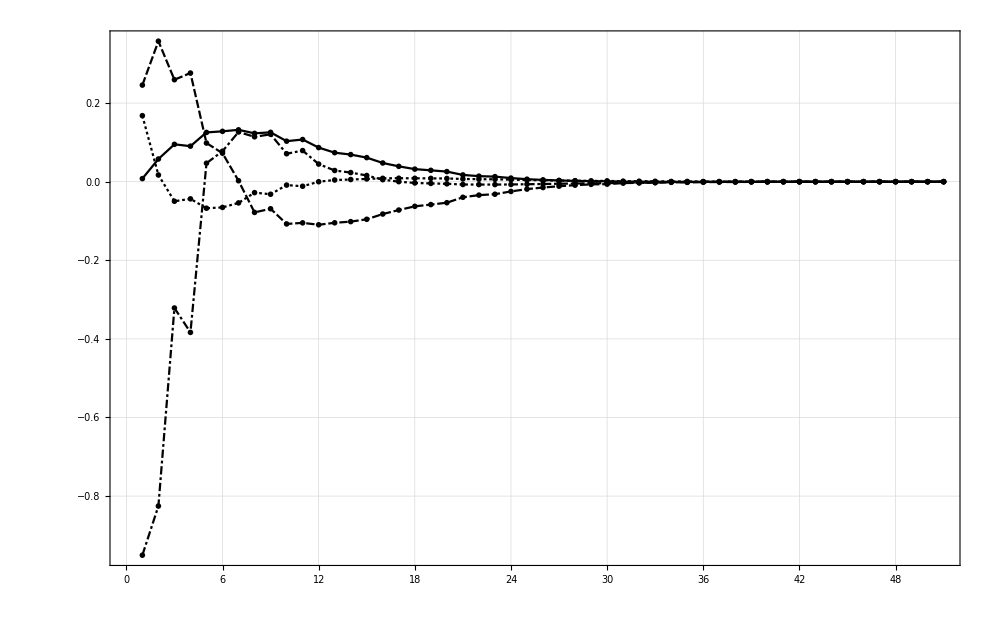

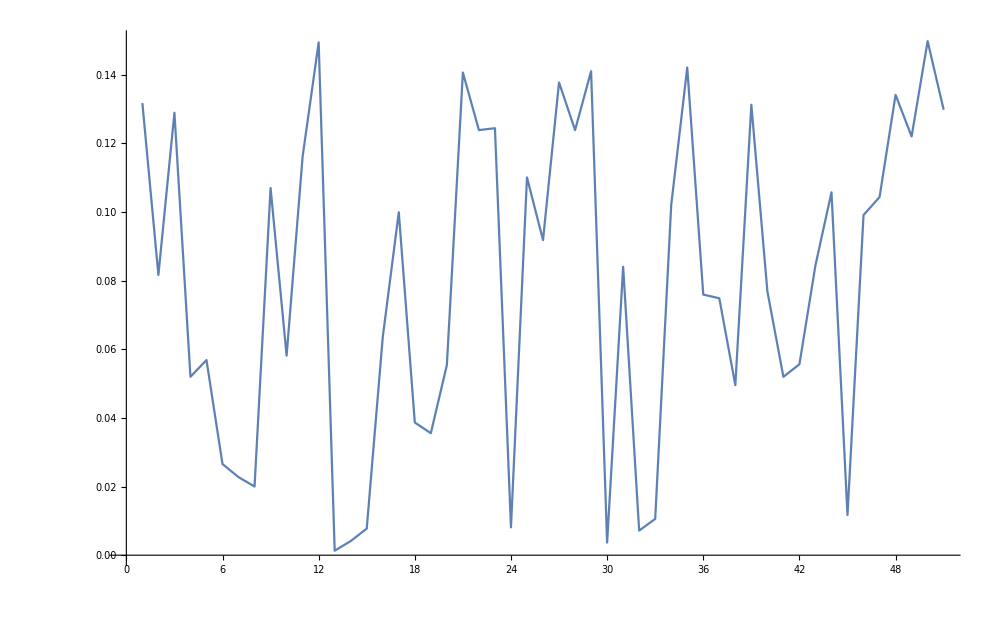

```mathematica
sampleData = Transpose[Table[solutionsLQR /. t->tau + .1 RandomReal[1.5], {tau, 0, 5, .1}]];
sampleDifference =  Table[.1 RandomReal[1.5], {tau, 0, 5, .1}];


 testPlot1 = ListLinePlot[
sampleData,
InterpolationOrder->1,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
ImageSize->{1000, 500},
PlotRange->Full,
FrameTicksStyle->Directive[FontSize->16],
FrameLabel ->{MaTeX["\\text{Tempo }(s)",Magnification->1.5], MaTeX["\\text{Velocità }\\left(\\frac m s\\right)",Magnification->1.5]}
]


ListLinePlot[sampleDifference]
```